## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initialize Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = False;
removeOutputFiles = False;

rxnName="ENO";
fitLabel=rxnName;
dataFileName="ENO";

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = False; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)
(*Q10 = 2.5; Average factor for biological systems*)

(* user will need to change this path *)
pathMASSef = "/home/mrama/Desktop/MASSef/";
kineticDataFileName =  "kinetic_data_MD.csv";

mainFolder = "ENO_param_inf2";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

{2pg,Null,Keq substrate}

{5.19,Keq value}

{2pg,Km or S05 substrate}

{0.0001,Km or S05 value}

{{{2pg,Null}},kcat substrates}

{330,kcat value}

((2pg)^c⇌h2o^c+pep^c)^ENO

Null; Null

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 2pg,Null | 5.19 | 4.9305
5.4495 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 2pg | 0.0001 | 0.000095
0.000105 | mg2 | 0.001
so4 | 0.001 | M | 8.1 | 30 | trishcl | 0.05 | cl | 0.1
k | 0.1

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 2pg | Null | 330 | 313.5
346.5 | 1/s | 8.1 | 30 | trishcl | 0.05 | cl | 0.1
k | 0.1

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1};
s05Priorities = Null;
kcatPriorities = {1};
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

((2pg)^c⇌h2o^c+pep^c)^ENO

Null; Null

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 2pg,Null | 5.19 | 4.9305
5.4495 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 2pg | 0.0001 | 0.000095
0.000105 | mg2 | 0.001
so4 | 0.001 | M | 8.1 | 30 | trishcl | 0.05 | cl | 0.1
k | 0.1

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 2pg | Null | 330 | 313.5
346.5 | 1/s | 8.1 | 30 | trishcl | 0.05 | cl | 0.1
k | 0.1

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_ENO[c] + 2pg[c] <=> E_ENO[c]&2pg",
				"E_ENO[c]&2pg <=> E_ENO[c]&pep",
				"E_ENO[c]&pep <=> E_ENO[c] + pep[c]"};

enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((ENO^c)_^+(2pg)^c⇌(ENO^c&(2pg)^c)_^)^ENO1,((ENO^c&pep^c)_^⇌(ENO^c)_^+pep^c)^ENO2,((ENO^c&(2pg)^c)_^⇌(ENO^c&pep^c)_^)^ENO3}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1=enzymeModel["Reactions"];
catalyticReactionsSetsList = {catalyticReactionsSet1}
```

{{((ENO^c)_^+(2pg)^c⇌(ENO^c&(2pg)^c)_^)^ENO1,((ENO^c&pep^c)_^⇌(ENO^c)_^+pep^c)^ENO2,((ENO^c&(2pg)^c)_^⇌(ENO^c&pep^c)_^)^ENO3}}

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=1;
simplifyFlag=True;
simplifyMaxTime=300;
assumedSaturatingConc=1;
(* for the flux equation regarding product inhibition *)
otherMetsReverseZeroSub={};
otherMetsForwardZeroSub={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList, inhibitionList, catalyticReactionsSetsList,
						 otherMetsReverseZeroSub, otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites, assumedSaturatingConc];
```

{(2pg)^c→0}

{pep^c→0}

{(2pg)^c→1}

{pep^c→1}

Added inhibition reactions:

{}

Loading flux equation...

Loading absolute rate forward equation...

Loading absolute rate reverse equation...

Loading relative rate forward equation...

Loading relative rate reverse equation...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

```mathematica
absoluteRateForward//Simplify
```

((2pg)^c ENO_total_Global k_ENO1^⟶ k_ENO2^⟶ k_ENO3^⟶)/(k_ENO1^⟵ (k_ENO2^⟶+k_ENO3^⟵)+k_ENO2^⟶ k_ENO3^⟶+(2pg)^c k_ENO1^⟶ (k_ENO2^⟶+k_ENO3^⟵+k_ENO3^⟶))

```mathematica
relativeRateForward//Simplify
```

{((2pg)^c (k_ENO1^⟵ (k_ENO2^⟶+k_ENO3^⟵)+k_ENO2^⟶ k_ENO3^⟶+k_ENO1^⟶ (k_ENO2^⟶+k_ENO3^⟵+k_ENO3^⟶)))/(k_ENO1^⟵ (k_ENO2^⟶+k_ENO3^⟵)+k_ENO2^⟶ k_ENO3^⟶+(2pg)^c k_ENO1^⟶ (k_ENO2^⟶+k_ENO3^⟵+k_ENO3^⟶))}

```mathematica
Values@Solve[absoluteRateForward==(absoluteRateForward/. (2pg)^c-> 1)/2, (2pg)^c][[1]][[1]]
```

(k_ENO1^⟵ k_ENO2^⟶+k_ENO1^⟵ k_ENO3^⟵+k_ENO2^⟶ k_ENO3^⟶)/(2 k_ENO1^⟵ k_ENO2^⟶+k_ENO1^⟶ k_ENO2^⟶+2 k_ENO1^⟵ k_ENO3^⟵+k_ENO1^⟶ k_ENO3^⟵+k_ENO1^⟶ k_ENO3^⟶+2 k_ENO2^⟶ k_ENO3^⟶)

## Simulate Data

```mathematica
enzymeModel["Reactions"]
```

{((ENO^c)_^+(2pg)^c⇌(ENO^c&(2pg)^c)_^)^ENO1,((ENO^c&pep^c)_^⇌(ENO^c)_^+pep^c)^ENO2,((ENO^c&(2pg)^c)_^⇌(ENO^c&pep^c)_^)^ENO3}

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={{1,( Subscript[k, ENO1]^⟶/Subscript[k, ENO1]^⟵)*(Subscript[k, ENO2]^⟶/Subscript[k, ENO2]^⟵), 3.6*10^-9,{1.7*10^-10, 8.*10^-8}}}; (*Define dKb ratio and respective value*)
customRatiosDataList
```

{{1,(k_ENO1^⟶ k_ENO2^⟶)/(k_ENO1^⟵ k_ENO2^⟵),3.6×10^-9,{1.7×10^-10,8.×10^-8}}}

### Simulate data without uncertainty

```mathematica
customRatiosDataList={{1,( Subscript[k, ENO1]^⟶/Subscript[k, ENO1]^⟵)*(Subscript[k, ENO2]^⟶/Subscript[k, ENO2]^⟵), 10.^-11,{1.7*10^-10, 8.*10^-8}}}; (*Define dKb ratio and respective value*)
customRatiosDataList
```

{{1,(k_ENO1^⟶ k_ENO2^⟶)/(k_ENO1^⟵ k_ENO2^⟵),1.×10^-11,{1.7×10^-10,8.×10^-8}}}

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,  fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

```mathematica
FilePrint@dataPathList
```

Priority	2pg[c]	pep[c]	param_ENO_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan2/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan2/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan2/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan2/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan2/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan2/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan2/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan2/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan2/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan2/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan2/input/haldaneRatio_1.txt"	5.19
1	0.00001	0	1	8.1	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan2/input/relRateFor_2pg.txt"	0.09090909090909091
1	0.00001584893192461114	0	1	8.1	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan2/input/relRateFor_2pg.txt"	0.13680688860321005
1	0.000025118864315095822	0	1	8.1	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan2/input/relRateFor_2pg.txt"	0.20076000891310186
1	0.000039810717055349695	0	1	8.1	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan2/input/relRateFor_2pg.txt"	0.2847472489508013
1	0.00006309573444801929	0	1	8.1	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan2/input/relRateFor_2pg.txt"	0.3868631798468568
1	0.0001	0	1	8.1	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan2/input/relRateFor_2pg.txt"	0.5
1	0.00015848931924611142	0	1	8.1	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan2/input/relRateFor_2pg.txt"	0.6131368201531432
1	0.0002511886431509582	0	1	8.1	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan2/input/relRateFor_2pg.txt"	0.7152527510491988
1	0.00039810717055349735	0	1	8.1	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan2/input/relRateFor_2pg.txt"	0.7992399910868982
1	0.000630957344480193	0	1	8.1	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan2/input/relRateFor_2pg.txt"	0.8631931113967899
1	0.001	0	1	8.1	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan2/input/relRateFor_2pg.txt"	0.9090909090909091
1	1	0	1	8.1	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan2/input/absRateFor.txt"	330
1	1	0	1	8.1	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan2/input/absRateFor.txt"	330
1	1	0	1	8.1	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan2/input/absRateFor.txt"	330
1	1	0	1	8.1	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan2/input/absRateFor.txt"	330
1	1	0	1	8.1	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan2/input/absRateFor.txt"	330
1	1	0	1	8.1	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan2/input/absRateFor.txt"	330
1	1	0	1	8.1	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan2/input/absRateFor.txt"	330
1	1	0	1	8.1	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan2/input/absRateFor.txt"	330
1	1	0	1	8.1	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan2/input/absRateFor.txt"	330
1	1	0	1	8.1	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan2/input/absRateFor.txt"	330
1	1	0	1	8.1	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan2/input/absRateFor.txt"	330
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan2/input/customRatio_1.txt"	1.e-11
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan2/input/customRatio_1.txt"	1.e-11
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan2/input/customRatio_1.txt"	1.e-11
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan2/input/customRatio_1.txt"	1.e-11
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan2/input/customRatio_1.txt"	1.e-11
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan2/input/customRatio_1.txt"	1.e-11
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan2/input/customRatio_1.txt"	1.e-11
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan2/input/customRatio_1.txt"	1.e-11
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan2/input/customRatio_1.txt"	1.e-11
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan2/input/customRatio_1.txt"	1.e-11
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan2/input/customRatio_1.txt"	1.e-11

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList];
```

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

«7 more identical outputs»

```mathematica
FilePrint[dataPathList[[1]]]
```

13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.09090909090909095
0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.1368068886032101
0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.20076000891310197
0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.2847472489508014
0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.38686317984685703
0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.5000000000000001
0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.6131368201531432
0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7152527510491988
0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7992399910868984
0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.86319311139679
0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.9090909090909091
0	0.00010091718583050879	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.09090909090909087
0	0.0001599429608251066	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.13680688860321003
0	0.0002534925097937858	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2007600089131016
0	0.0004017585531120535	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2847472489508014
0	0.0006367443958403206	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.386863179846857
0	0.001009171858305088	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.4999999999999999
0	0.001599429608251066	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.613136820153143
0	0.0025349250979378583	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7152527510491984
0	0.0040175855311205344	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7992399910868982
0	0.006367443958403205	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.8631931113967901
0	0.01009171858305088	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.9090909090909091
0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.0909090909090909
0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.13680688860321005
0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.20076000891310167
0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.2847472489508014
0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.3868631798468568
0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.5
0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.6131368201531432
0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7152527510491987
0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7992399910868982
0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.86319311139679
0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.9090909090909091
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.

### Parameter influence

```mathematica
dataFileName = "ENO_all";
KeqListTemp=KeqList;
kmListTemp= kmList;
kcatListTemp = kcatList;
customRatiosDataListTemp=customRatiosDataList;

{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,fitLabel,  haldaneRatiosList, KeqListTemp, kmListTemp, s05List, kcatListTemp, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataListTemp, assumedSaturatingConc];

dataFileName = "ENO_dKd";
KeqListTemp=KeqList;
kmListTemp= kmList;
kcatListTemp = kcatList;
customRatiosDataListTemp={};

{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, fitLabel, haldaneRatiosList, KeqListTemp, kmListTemp, s05List, kcatListTemp, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataListTemp, assumedSaturatingConc];

dataFileName = "ENO_Keq";
KeqListTemp={};
kmListTemp= kmList;
kcatListTemp = kcatList;
customRatiosDataListTemp=customRatiosDataList;

{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, fitLabel, haldaneRatiosList, KeqListTemp, kmListTemp, s05List, kcatListTemp, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataListTemp, assumedSaturatingConc];

dataFileName = "ENO_Km";
KeqListTemp=KeqList;
kmListTemp={};
kcatListTemp = kcatList;
customRatiosDataListTemp=customRatiosDataList;

{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, fitLabel, haldaneRatiosList, KeqListTemp, kmListTemp, s05List, kcatListTemp, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataListTemp, assumedSaturatingConc];

dataFileName = "ENO_kcat";
KeqListTemp=KeqList;
kmListTemp=kmList;
kcatListTemp = {};
customRatiosDataListTemp=customRatiosDataList;

{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,fitLabel,  haldaneRatiosList, KeqListTemp, kmListTemp, s05List, kcatListTemp, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataListTemp, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating custom ratios data...

### Parameter scan

```mathematica
paramScanList={{"customRatio",1,{10.^-12,10.^-11,10.^-10,10.^-9,10.^-8, 10.^-7,10.^-6,10.^-5,0.0001,0.001, 0.01,0.1, 1.0,  10, 100, 1000, 10000, 10^5,10^6,10^7, 10^8, 10^9, 10^10,10^11,10^12}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, fitLabel,
						  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

```mathematica
Length@dataPathList
```

26

```mathematica
FilePrint[dataPathList[[26]]]
```

Priority	2pg[c]	pep[c]	param_ENO_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/haldaneRatio_1.txt"	5.19
1	0.00001	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/relRateFor_2pg.txt"	0.09090909090909091
1	0.00001584893192461114	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/relRateFor_2pg.txt"	0.13680688860321005
1	0.000025118864315095822	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/relRateFor_2pg.txt"	0.20076000891310186
1	0.000039810717055349695	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/relRateFor_2pg.txt"	0.2847472489508013
1	0.00006309573444801929	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/relRateFor_2pg.txt"	0.3868631798468568
1	0.0001	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/relRateFor_2pg.txt"	0.5
1	0.00015848931924611142	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/relRateFor_2pg.txt"	0.6131368201531432
1	0.0002511886431509582	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/relRateFor_2pg.txt"	0.7152527510491988
1	0.00039810717055349735	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/relRateFor_2pg.txt"	0.7992399910868982
1	0.000630957344480193	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/relRateFor_2pg.txt"	0.8631931113967899
1	0.001	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/relRateFor_2pg.txt"	0.9090909090909091
1	0.01	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/absRateFor.txt"	330
1	0.01	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/absRateFor.txt"	330
1	0.01	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/absRateFor.txt"	330
1	0.01	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/absRateFor.txt"	330
1	0.01	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/absRateFor.txt"	330
1	0.01	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/absRateFor.txt"	330
1	0.01	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/absRateFor.txt"	330
1	0.01	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/absRateFor.txt"	330
1	0.01	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/absRateFor.txt"	330
1	0.01	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/absRateFor.txt"	330
1	0.01	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/absRateFor.txt"	330
1.	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/customRatio_1.txt"	1.e12
1.	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/customRatio_1.txt"	1.e12
1.	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/customRatio_1.txt"	1.e12
1.	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/customRatio_1.txt"	1.e12
1.	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/customRatio_1.txt"	1.e12
1.	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/customRatio_1.txt"	1.e12
1.	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/customRatio_1.txt"	1.e12
1.	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/customRatio_1.txt"	1.e12
1.	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/customRatio_1.txt"	1.e12
1.	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/customRatio_1.txt"	1.e12
1.	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/customRatio_1.txt"	1.e12

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
fitLabel="10-11_fit"
```

10-11_fit

```mathematica
numTrials=100;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numTrials,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

## Run the Fitting Algorithms

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numTrials, dataPathList]
```

best_fit: 0.696928147789
best_fit: 0.979954200549
best_fit: 0.66921170808
best_fit: 1.07362140851
best_fit: 1.07865446034
best_fit: 1.04526812784
best_fit: 0.804277386819
best_fit: 0.684483441305
best_fit: 1.0896662564
best_fit: 1.05614338524
best_fit: 0.491095241375
best_fit: 0.831956302972
best_fit: 0.890110431444
best_fit: 0.770506543652
best_fit: 0.621748959838
best_fit: 0.413785947975
best_fit: 0.858661321155
best_fit: 0.474661091528
best_fit: 1.06963375038
best_fit: 0.77184785683
best_fit: 0.545617576636
best_fit: 0.71279259308
best_fit: 0.69482841901
best_fit: 1.05613808618
best_fit: 1.00018332326
best_fit: 1.03192155178
best_fit: 1.08593472773
best_fit: 0.132936073134
best_fit: 0.968879246028
best_fit: 0.89821373501
best_fit: 0.934994312673
best_fit: 0.826872810527
best_fit: 1.06177345606
best_fit: 0.906807969211
best_fit: 0.743983406596
best_fit: 0.911504645062
best_fit: 0.757941051168
best_fit: 1.09399086724
best_fit: 0.746855154593
best_fit: 1.00332839696
best_fit: 0.535463114598
best_fit: 1.09785635394
best_fit: 1.06253794332
best_fit: 1.06714519842
best_fit: 0.277017796195
best_fit: 1.0777134883
best_fit: 0.246490313232
best_fit: 0.143340668392
best_fit: 0.629415224852
best_fit: 1.07352705365
best_fit: 1.08574645593
best_fit: 1.07117277929
best_fit: 1.07232850731
best_fit: 1.01071574034
best_fit: 0.924997252789
best_fit: 0.970788821749
best_fit: 0.663657850177
best_fit: 0.989491423721
best_fit: 0.94195485027
best_fit: 1.06946690556
best_fit: 0.294066574193
best_fit: 1.0875583505
best_fit: 1.08399341938
best_fit: 0.251184103988
best_fit: 1.01236249863
best_fit: 0.973008002668
best_fit: 1.07041180345
best_fit: 1.00749630558
best_fit: 0.322101370473
best_fit: 0.969888968128
best_fit: 1.08940179323
best_fit: 0.323127527586
best_fit: 0.908036144574
best_fit: 0.989935896327
best_fit: 1.00815422567
best_fit: 1.06858769836
best_fit: 0.853242822944
best_fit: 1.03084015609
best_fit: 0.971216753289
best_fit: 0.466821559335
best_fit: 0.690025973734
best_fit: 1.05556494846
best_fit: 0.580826111487
best_fit: 1.01996835623
best_fit: 0.969522126973
best_fit: 1.00523605497
best_fit: 0.374205411531
best_fit: 1.08340307429
best_fit: 0.851127557671
best_fit: 0.838405040263
best_fit: 1.09477848086
best_fit: 0.899523691011
best_fit: 0.774675335779
best_fit: 0.933417951143
best_fit: 0.699806819945
best_fit: 1.01308167871
best_fit: 1.05047901518
best_fit: 0.848945351987
best_fit: 1.06385232219
best_fit: 0.858178925146

$Aborted

## Evaluate fit results

```mathematica
(*no uncertainty or parameter scan*)
lmaResultsFileNameNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(*with uncertainty or parameter scan*)
datasetI=2;
lmaResultsFileNameNew=StringTake[lmaResultsFileName,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

StringTake::strse: String or list of strings expected at position 1 in StringTake[lmaResultsFileName,1;;-5].

StringJoin::string: String expected at position 1 in StringTake[lmaResultsFileName,1;;-5]<>_2.txt.

Part::partd: Part specification /home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test_kcatKm_defs/input/TPI_general.dat⟦2⟧ is longer than depth of object.

```mathematica
dataFilePath
```

/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test_kcatKm_defs/input/TPI_general.dat

```mathematica
flagFitType = "log_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNameNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, fitLabel<>"_"<>flagFitType];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 5.82458×10^-10 | 3.39257×10^-19 | 6.96061×10^-9 | 1.34116×10^-7 | 5.19 | 5.19
1 | haldaneRatio_1 | 5.82458×10^-10 | 3.39257×10^-19 | 6.96061×10^-9 | 1.34116×10^-7 | 5.19 | 5.19
1 | haldaneRatio_1 | 5.82458×10^-10 | 3.39257×10^-19 | 6.96061×10^-9 | 1.34116×10^-7 | 5.19 | 5.19
1 | haldaneRatio_1 | 5.82458×10^-10 | 3.39257×10^-19 | 6.96061×10^-9 | 1.34116×10^-7 | 5.19 | 5.19
1 | haldaneRatio_1 | 5.82458×10^-10 | 3.39257×10^-19 | 6.96061×10^-9 | 1.34116×10^-7 | 5.19 | 5.19
1 | haldaneRatio_1 | 5.82458×10^-10 | 3.39257×10^-19 | 6.96061×10^-9 | 1.34116×10^-7 | 5.19 | 5.19
1 | haldaneRatio_1 | 5.82458×10^-10 | 3.39257×10^-19 | 6.96061×10^-9 | 1.34116×10^-7 | 5.19 | 5.19
1 | haldaneRatio_1 | 5.82458×10^-10 | 3.39257×10^-19 | 6.96061×10^-9 | 1.34116×10^-7 | 5.19 | 5.19
1 | haldaneRatio_1 | 5.82458×10^-10 | 3.39257×10^-19 | 6.96061×10^-9 | 1.34116×10^-7 | 5.19 | 5.19
1 | haldaneRatio_1 | 5.82458×10^-10 | 3.39257×10^-19 | 6.96061×10^-9 | 1.34116×10^-7 | 5.19 | 5.19
1 | haldaneRatio_1 | 5.82458×10^-10 | 3.39257×10^-19 | 6.96061×10^-9 | 1.34116×10^-7 | 5.19 | 5.19
1 | relRateFor_2pg | 0.000016127 | 2.60081×10^-10 | 3.37574×10^-6 | 0.00371331 | 0.0909091 | 0.0909057
1 | relRateFor_2pg | 0.0000131201 | 1.72138×10^-10 | 4.1329×10^-6 | 0.00302097 | 0.136807 | 0.136803
1 | relRateFor_2pg | 8.93035×10^-6 | 7.97512×10^-11 | 4.12816×10^-6 | 0.00205627 | 0.20076 | 0.200756
1 | relRateFor_2pg | 3.42802×10^-6 | 1.17513×10^-11 | 2.24759×10^-6 | 0.000789327 | 0.284747 | 0.284745
1 | relRateFor_2pg | 3.26209×10^-6 | 1.06412×10^-11 | 2.90584×10^-6 | 0.000751127 | 0.386863 | 0.386866
1 | relRateFor_2pg | 0.0000106744 | 1.13942×10^-10 | 0.0000122895 | 0.00245789 | 0.5 | 0.500012
1 | relRateFor_2pg | 0.0000180867 | 3.2713×10^-10 | 0.0000255354 | 0.00416471 | 0.613137 | 0.613162
1 | relRateFor_2pg | 0.0000247772 | 6.13909×10^-10 | 0.0000408075 | 0.00570532 | 0.715253 | 0.715294
1 | relRateFor_2pg | 0.0000302799 | 9.16875×10^-10 | 0.0000557267 | 0.00697246 | 0.79924 | 0.799296
1 | relRateFor_2pg | 0.0000344701 | 1.18819×10^-9 | 0.0000685147 | 0.00793736 | 0.863193 | 0.863262
1 | relRateFor_2pg | 0.0000374774 | 1.40455×10^-9 | 0.0000784532 | 0.00862986 | 0.909091 | 0.909169
1 | absRateFor | 6.67373×10^-10 | 4.45387×10^-19 | 5.07105×10^-7 | 1.53668×10^-7 | 330 | 330.
1 | absRateFor | 6.67373×10^-10 | 4.45387×10^-19 | 5.07105×10^-7 | 1.53668×10^-7 | 330 | 330.
1 | absRateFor | 6.67373×10^-10 | 4.45387×10^-19 | 5.07105×10^-7 | 1.53668×10^-7 | 330 | 330.
1 | absRateFor | 6.67373×10^-10 | 4.45387×10^-19 | 5.07105×10^-7 | 1.53668×10^-7 | 330 | 330.
1 | absRateFor | 6.67373×10^-10 | 4.45387×10^-19 | 5.07105×10^-7 | 1.53668×10^-7 | 330 | 330.
1 | absRateFor | 6.67373×10^-10 | 4.45387×10^-19 | 5.07105×10^-7 | 1.53668×10^-7 | 330 | 330.
1 | absRateFor | 6.67373×10^-10 | 4.45387×10^-19 | 5.07105×10^-7 | 1.53668×10^-7 | 330 | 330.
1 | absRateFor | 6.67373×10^-10 | 4.45387×10^-19 | 5.07105×10^-7 | 1.53668×10^-7 | 330 | 330.
1 | absRateFor | 6.67373×10^-10 | 4.45387×10^-19 | 5.07105×10^-7 | 1.53668×10^-7 | 330 | 330.
1 | absRateFor | 6.67373×10^-10 | 4.45387×10^-19 | 5.07105×10^-7 | 1.53668×10^-7 | 330 | 330.
1 | absRateFor | 6.67373×10^-10 | 4.45387×10^-19 | 5.07105×10^-7 | 1.53668×10^-7 | 330 | 330.
1 | customRatio_1 | 1.23271×10^-9 | 1.51958×10^-18 | 1.02183×10^-17 | 2.83843×10^-7 | 3.6×10^-9 | 3.6×10^-9
1 | customRatio_1 | 1.23271×10^-9 | 1.51958×10^-18 | 1.02183×10^-17 | 2.83843×10^-7 | 3.6×10^-9 | 3.6×10^-9
1 | customRatio_1 | 1.23271×10^-9 | 1.51958×10^-18 | 1.02183×10^-17 | 2.83843×10^-7 | 3.6×10^-9 | 3.6×10^-9
1 | customRatio_1 | 1.23271×10^-9 | 1.51958×10^-18 | 1.02183×10^-17 | 2.83843×10^-7 | 3.6×10^-9 | 3.6×10^-9
1 | customRatio_1 | 1.23271×10^-9 | 1.51958×10^-18 | 1.02183×10^-17 | 2.83843×10^-7 | 3.6×10^-9 | 3.6×10^-9
1 | customRatio_1 | 1.23271×10^-9 | 1.51958×10^-18 | 1.02183×10^-17 | 2.83843×10^-7 | 3.6×10^-9 | 3.6×10^-9
1 | customRatio_1 | 1.23271×10^-9 | 1.51958×10^-18 | 1.02183×10^-17 | 2.83843×10^-7 | 3.6×10^-9 | 3.6×10^-9
1 | customRatio_1 | 1.23271×10^-9 | 1.51958×10^-18 | 1.02183×10^-17 | 2.83843×10^-7 | 3.6×10^-9 | 3.6×10^-9
1 | customRatio_1 | 1.23271×10^-9 | 1.51958×10^-18 | 1.02183×10^-17 | 2.83843×10^-7 | 3.6×10^-9 | 3.6×10^-9
1 | customRatio_1 | 1.23271×10^-9 | 1.51958×10^-18 | 1.02183×10^-17 | 2.83843×10^-7 | 3.6×10^-9 | 3.6×10^-9
1 | customRatio_1 | 1.23271×10^-9 | 1.51958×10^-18 | 1.02183×10^-17 | 2.83843×10^-7 | 3.6×10^-9 | 3.6×10^-9

### Simulated Data and Best Fit Data Plot

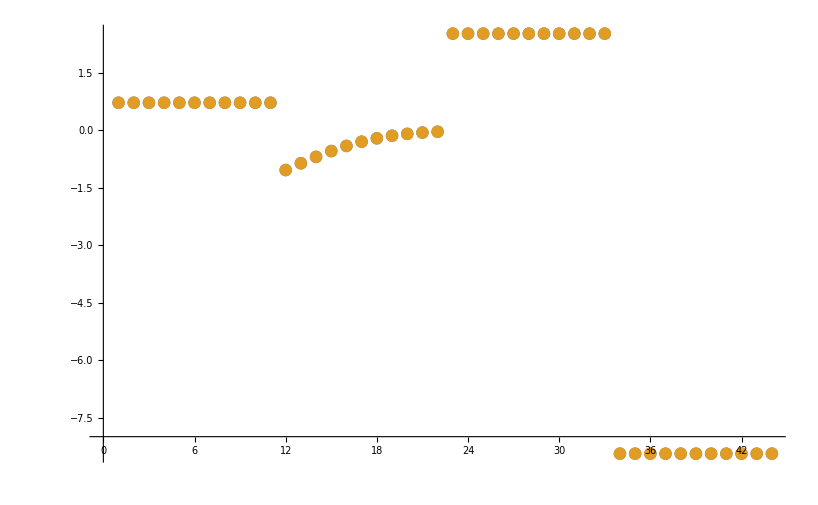

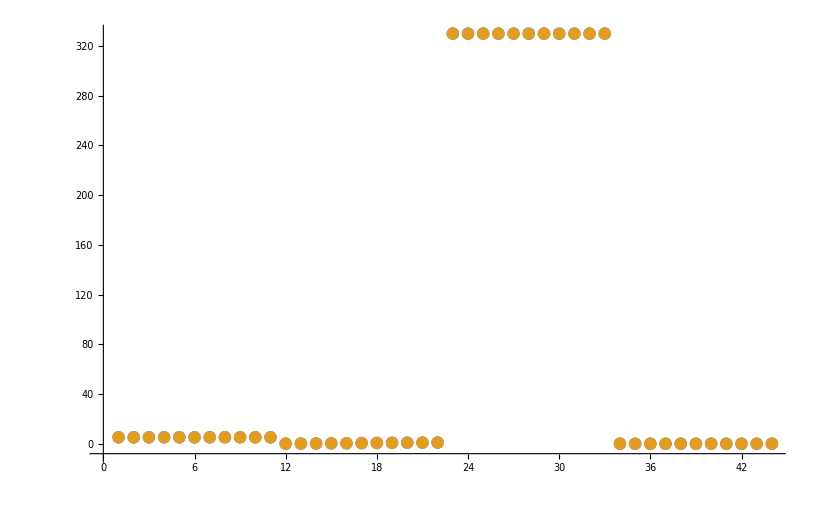

```mathematica
datasetI=50;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}, AxesOrigin->{0,-8}]
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1
assumedSaturatingConc=1
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[1,2]]]
```

#### Export rate back calculated parameter error distribution

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
nRateSets=100;
rateConstList=Import["/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/fit_ENO2/output/treated_data/rateconst_ENO_"<>fitLabel<>"_"<>flagFitType<>".csv", "TSV"];

predictedParamsErrorList=Table[

(*paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[rateSetI,2]]];*)
paramFitSub=Thread[rateConstsSub[[All,1]]->rateConstList[[rateSetI,2;;]]];

{rateConstList[[rateSetI,1]],
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse, metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName][[2,3]],
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc][[2,3]],
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]],  paramFitSub][[2,3]],
backCalculateRatios[customRatiosDataList[[1,2]],customRatiosDataList[[1,3]], paramFitSub][[2,3]]}//Flatten,

{rateSetI, 1, nRateSets}];

predictedParamsErrorList=Insert[predictedParamsErrorList,{"ssd","Km_g3p","kcat_f","Keq"} , 1];
predictedParamsErrorList=Insert[predictedParamsErrorList,{0,kmList[[1]][[3]],kcatList[[1]][[3]], KeqList[[1]][[3]]}  ,2];
Export[outputPath<>"/treated_data/predicted_params_error_distribution_"<>fitLabel<>"_"<>flagFitType<>".csv",predictedParamsErrorList,"CSV"];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

## Evaluate fit results for param_scan

```mathematica
fileListSub
```

{/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan/input/absRateFor.txt→((2pg)^c ENO_total_Global k_ENO1^⟶ k_ENO2^⟶ k_ENO3^⟶)/(k_ENO1^⟵ (k_ENO2^⟶+k_ENO3^⟵)+k_ENO2^⟶ k_ENO3^⟶+(2pg)^c k_ENO1^⟶ (k_ENO2^⟶+k_ENO3^⟵+k_ENO3^⟶)),/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan/input/absRateRev.txt→(pep^c ENO_total_Global k_ENO1^⟵ k_ENO2^⟵ k_ENO3^⟵)/(k_ENO1^⟵ (k_ENO2^⟶+k_ENO3^⟵)+k_ENO2^⟶ k_ENO3^⟶+pep^c k_ENO2^⟵ (k_ENO1^⟵+k_ENO3^⟵+k_ENO3^⟶)),/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan/input/relRateFor_2pg.txt→((2pg)^c (k_ENO1^⟵ (k_ENO2^⟶+k_ENO3^⟵)+k_ENO2^⟶ k_ENO3^⟶+k_ENO1^⟶ (k_ENO2^⟶+k_ENO3^⟵+k_ENO3^⟶)))/(k_ENO1^⟵ (k_ENO2^⟶+k_ENO3^⟵)+k_ENO2^⟶ k_ENO3^⟶+(2pg)^c k_ENO1^⟶ (k_ENO2^⟶+k_ENO3^⟵+k_ENO3^⟶)),/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan/input/relRateRev_pep.txt→(pep^c (k_ENO1^⟵ (k_ENO2^⟵+k_ENO2^⟶+k_ENO3^⟵)+k_ENO2^⟶ k_ENO3^⟶+k_ENO2^⟵ (k_ENO3^⟵+k_ENO3^⟶)))/(k_ENO1^⟵ (k_ENO2^⟶+k_ENO3^⟵)+k_ENO2^⟶ k_ENO3^⟶+pep^c k_ENO2^⟵ (k_ENO1^⟵+k_ENO3^⟵+k_ENO3^⟶)),/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan/input/haldaneRatio_1.txt→(k_ENO1^⟶ k_ENO2^⟶ k_ENO3^⟶)/(k_ENO1^⟵ k_ENO2^⟵ k_ENO3^⟵),/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan/input/customRatio_1.txt→(k_ENO1^⟶ k_ENO2^⟶)/(k_ENO1^⟵ k_ENO2^⟵)}

```mathematica
outputPath
```

/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_scan2/output

```mathematica
inou
```

```mathematica
paramScanList={{"customRatio",1,{10.^-12,10.^-11,10.^-10,10.^-9,10.^-8, 10.^-7,10.^-6,10.^-5,0.0001,0.001, 0.01,0.1, 1.0,  10, 100, 1000, 10000, 10^5,10^6,10^7, 10^8, 10^9, 10^10,10^11,10^12}}};
nEnsembles = 10;

flagFitType = "log_ssd";
```

```mathematica
errorList = {};

Do[
Do[
fitDescription = paramScan[[1]] <>"_"<>ToString[paramScan[[2]]]<>"_"<> ToString[N@AccountingForm[paramVal]];

ssdList = 
Table[

lmaResultsFileNew = FileNameJoin[{outputPath, "raw", "lmaResults_"<> fitDescription<> "_"<>ToString@ensembleI<> ".txt"}, OperatingSystem->$OperatingSystem];
dataFilePath  = FileNameJoin[{inputPath,  "ENO_"<> fitDescription<>".dat"}, OperatingSystem->$OperatingSystem];

{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, fitDescription<>"_"<>ToString[ensembleI]];


ToString[N@AccountingForm[filteredDataList[[1,1]]]],

{ensembleI, Range[nEnsembles]}];

Print[ssdList];
AppendTo[errorList, Flatten@{ToString[N@AccountingForm[paramVal]], ssdList}];,

{paramVal, paramScan[[3]]}];,
{paramScan, paramScanList}];

Export[ FileNameJoin[{outputPath, "treated_data", "param_scan_ssd.csv"}, OperatingSystem->$OperatingSystem],errorList, "TSV"];
```

{17.5521,17.5521,17.5521,17.5521,17.5521,17.5521,17.5521,17.5521,17.5521,17.5521}

{8.3958,8.3958,8.3958,8.3958,8.3958,8.3958,8.3958,8.3958,8.3958,8.3958}

{2.65589,2.65589,2.65589,2.65589,2.65589,2.65589,2.65589,2.65589,2.65589,2.65589}

{0.161003,0.161003,0.161003,0.161003,0.161003,0.161003,0.161003,0.161003,0.161003,0.161003}

{0.00000000509896,0.00000000509896,0.00000000509896,0.00000000509896,0.00000000509896,0.00000000509896,0.00000000509896,0.00000000509896,0.00000000509896,0.00000000509896}

{0.00000000509896,0.00000000509896,0.00000000509896,0.00000000509896,0.00000000509896,0.00000000509896,0.00000000509896,0.00000000509896,0.00000000509896,0.00000000509896}

{0.00000000509896,0.00000000509896,0.00000000509896,0.00000000509896,0.00000000509896,0.00000000509896,0.00000000509896,0.00000000509896,0.00000000509896,0.00000000509896}

«12 more identical outputs»

{0.0399798,0.0399798,0.0399798,0.0399798,0.0399798,0.0399798,0.0399798,0.0399798,0.0399798,0.0399798}

{4.47239,4.47239,4.47239,4.47239,4.47239,4.47239,4.47239,4.47239,4.47239,4.47239}

{16.2381,16.2381,16.2381,16.2381,16.2381,16.2381,16.2381,16.2381,16.2381,16.2381}

{35.3372,35.3372,35.3372,35.3372,35.3372,35.3372,35.3372,35.3372,35.3372,35.3372}

{61.7696,61.7696,61.7696,61.7696,61.7696,61.7696,61.7696,61.7696,61.7696,61.7696}

{95.5354,95.5354,95.5354,95.5354,95.5354,95.5354,95.5354,95.5354,95.5354,95.5354}

```mathematica
errorList//TableForm
```

0.000000000001 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804
0.00000000001 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804
0.0000000001 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804
0.000000001 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804
0.00000001 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804
0.0000001 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804
0.000001 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119805
0.00001 | 0.0000000119807 | 0.0000000119806 | 0.0000000119804 | 0.0000000119809 | 0.0000000119808 | 0.0000000119804 | 0.000000011981 | 0.0000000119804 | 0.0000000119806 | 0.0000000119806
0.0001 | 0.0000000119805 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804
0.001 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804
0.01 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804
0.1 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804
1. | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804
10. | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804
100. | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804
1000. | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804
10000. | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804
100000. | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804
1000000. | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804 | 0.0000000119804
10000000. | 21.881 | 21.8842 | 21.8816 | 21.8809 | 21.916 | 21.8838 | 21.9193 | 21.8831 | 21.8823 | 21.8953
100000000. | 39117.5 | 39117.3 | 39117.4 | 39117.6 | 39117.3 | 39117.7 | 39117.1 | 39117.5 | 39117.6 | 39116.9
1000000000. | 943323. | 943322. | 943325. | 943324. | 943323. | 943322. | 943324. | 943322. | 943322. | 943319.
10000000000. | 1193035. | 1193035. | 1193035. | 1193035. | 1193035. | 1193035. | 1193035. | 1193035. | 1193035. | 1193035.
100000000000. | 1197682. | 1197682. | 1197682. | 1197683. | 1197683. | 1197682. | 1197683. | 1197683. | 1197683. | 1197683.
1000000000000. | 1197882. | 1197882. | 1197883. | 1197882. | 1197883. | 1197882. | 1197882. | 1197882. | 1197882. | 1197883.

#### Export rate back calculated parameter error distribution

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
nRateSets=100;

Do[

Do[
rateConstList=Import[outputPath<>"/treated_data/rateconst_ENO_customRatio_1_"<> ToString[N@AccountingForm[paramVal]]<>"_"<>ToString[ensembleI]<>".csv", "TSV"];

predictedParamsErrorList=Table[

(*paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[rateSetI,2]]];*)
paramFitSub=Thread[rateConstsSub[[All,1]]->rateConstList[[rateSetI,2;;]]];

{rateConstList[[rateSetI,1]],
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse, metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName][[2;;,3]],
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc][[2,3]],
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]],  paramFitSub][[2,3]],
backCalculateRatios[customRatiosDataList[[1,2]],paramVal,  paramFitSub][[2,3]]}//Flatten,

{rateSetI, 1, nRateSets}];

predictedParamsErrorList=Insert[predictedParamsErrorList,{"ssd","Km_2pg", "kcat_f","Keq", "dKd"} , 1];
predictedParamsErrorList=Insert[predictedParamsErrorList,{0,kmList[[1]][[3]],kcatList[[1]][[3]], KeqList[[1]][[3]], paramVal}  ,2];
Export[outputPath<>"/treated_data/predicted_params_error_distribution_"<> ToString[N@AccountingForm[paramVal]]<>"_"<>ToString[ensembleI]<>"_"<>flagFitType<>".csv",predictedParamsErrorList,"CSV"];,

{ensembleI, Range[nEnsembles]}];,

{paramVal, paramScanList[[1,3]]}];


Do[

Do[
rateConstList=Import[outputPath<>"/treated_data/rateconst_ENO_customRatio_1_"<> ToString[N@AccountingForm[paramVal]]<>"_"<>ToString[ensembleI]<>".csv", "TSV"];

predictedParamsErrorList=Table[

(*paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[rateSetI,2]]];*)
paramFitSub=Thread[rateConstsSub[[All,1]]->rateConstList[[rateSetI,2;;]]];

{rateConstList[[rateSetI,1]],
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse, metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName][[2;;,2]],
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc][[2,2]],
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]],  paramFitSub][[2,2]],
backCalculateRatios[customRatiosDataList[[1,2]],paramVal,  paramFitSub][[2,2]]}//Flatten,

{rateSetI, 1, nRateSets}];

predictedParamsErrorList=Insert[predictedParamsErrorList,{"ssd","Km_2pg", "kcat_f","Keq", "dKd"} , 1];
predictedParamsErrorList=Insert[predictedParamsErrorList,{0,kmList[[1]][[3]],kcatList[[1]][[3]], KeqList[[1]][[3]], paramVal}  ,2];
Export[outputPath<>"/treated_data/predicted_params_distribution_"<> ToString[N@AccountingForm[paramVal]]<>"_"<>ToString[ensembleI]<>"_"<>flagFitType<>".csv",predictedParamsErrorList,"CSV"];,

{ensembleI, Range[nEnsembles]}];,

{paramVal, paramScanList[[1,3]]}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

### Simulated Data and Best Fit Data Plot

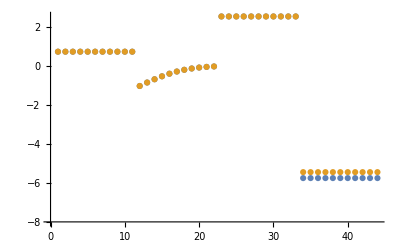

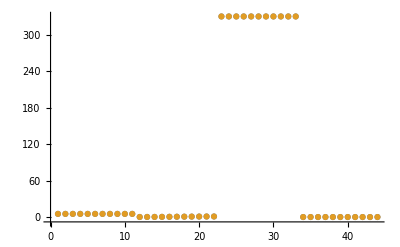

```mathematica
fitI=1;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[fitI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[fitI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution



```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```



```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```



```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```



```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

data value | predicted value | error in %
0.000045 | 0.000045 | 1.21792×10^-9
0.00089 | 0.00089 | 1.07241×10^-9
0.00053 | 0.00053 | 1.84462×10^-9

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
268 | 268. | 5.51572×10^-10

```mathematica
backCalculateRatios[customRatiosDataList[[1]][[2]], customRatiosDataList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
425. | 425. | 3.88996×10^-10

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.408 | 0.408 | 4.88403×10^-10

## Evaluate fit results for param_inf

```mathematica
paramList={"all", "dKd", "kcat", "Keq", "Km"};
nEnsembles = 99;

flagFitType = "log_ssd";

Do[
Do[

fitDescription = param <>"_"<>ToString[fitI];

lmaResultsFileNew = FileNameJoin[{outputPath, "raw", "lmaResults_"<> fitDescription<> ".txt"}, OperatingSystem->$OperatingSystem];
dataFilePath  = FileNameJoin[{inputPath,  "ENO_"<> param<> ".dat"}, OperatingSystem->$OperatingSystem];

{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, fitDescription];,

{fitI, 0, nEnsembles}],
{param, paramList}];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 6.54143×10^-12 | 4.27904×10^-23 | 7.81721×10^-11 | 1.50621×10^-9 | 5.19 | 5.19
1 | haldaneRatio_1 | 6.54143×10^-12 | 4.27904×10^-23 | 7.81721×10^-11 | 1.50621×10^-9 | 5.19 | 5.19
1 | haldaneRatio_1 | 6.54143×10^-12 | 4.27904×10^-23 | 7.81721×10^-11 | 1.50621×10^-9 | 5.19 | 5.19
1 | haldaneRatio_1 | 6.54143×10^-12 | 4.27904×10^-23 | 7.81721×10^-11 | 1.50621×10^-9 | 5.19 | 5.19
1 | haldaneRatio_1 | 6.54143×10^-12 | 4.27904×10^-23 | 7.81721×10^-11 | 1.50621×10^-9 | 5.19 | 5.19
1 | haldaneRatio_1 | 6.54143×10^-12 | 4.27904×10^-23 | 7.81721×10^-11 | 1.50621×10^-9 | 5.19 | 5.19
1 | haldaneRatio_1 | 6.54143×10^-12 | 4.27904×10^-23 | 7.81721×10^-11 | 1.50621×10^-9 | 5.19 | 5.19
1 | haldaneRatio_1 | 6.54143×10^-12 | 4.27904×10^-23 | 7.81721×10^-11 | 1.50621×10^-9 | 5.19 | 5.19
1 | haldaneRatio_1 | 6.54143×10^-12 | 4.27904×10^-23 | 7.81721×10^-11 | 1.50621×10^-9 | 5.19 | 5.19
1 | haldaneRatio_1 | 6.54143×10^-12 | 4.27904×10^-23 | 7.81721×10^-11 | 1.50621×10^-9 | 5.19 | 5.19
1 | haldaneRatio_1 | 6.54143×10^-12 | 4.27904×10^-23 | 7.81721×10^-11 | 1.50621×10^-9 | 5.19 | 5.19
1 | absRateFor | 3.55271×10^-15 | 1.26218×10^-29 | 2.38742×10^-12 | 7.23462×10^-13 | 330 | 330.
1 | absRateFor | 3.55271×10^-15 | 1.26218×10^-29 | 2.38742×10^-12 | 7.23462×10^-13 | 330 | 330.
1 | absRateFor | 3.55271×10^-15 | 1.26218×10^-29 | 2.38742×10^-12 | 7.23462×10^-13 | 330 | 330.
1 | absRateFor | 3.55271×10^-15 | 1.26218×10^-29 | 2.38742×10^-12 | 7.23462×10^-13 | 330 | 330.
1 | absRateFor | 3.55271×10^-15 | 1.26218×10^-29 | 2.38742×10^-12 | 7.23462×10^-13 | 330 | 330.
1 | absRateFor | 3.55271×10^-15 | 1.26218×10^-29 | 2.38742×10^-12 | 7.23462×10^-13 | 330 | 330.
1 | absRateFor | 3.55271×10^-15 | 1.26218×10^-29 | 2.38742×10^-12 | 7.23462×10^-13 | 330 | 330.
1 | absRateFor | 3.55271×10^-15 | 1.26218×10^-29 | 2.38742×10^-12 | 7.23462×10^-13 | 330 | 330.
1 | absRateFor | 3.55271×10^-15 | 1.26218×10^-29 | 2.38742×10^-12 | 7.23462×10^-13 | 330 | 330.
1 | absRateFor | 3.55271×10^-15 | 1.26218×10^-29 | 2.38742×10^-12 | 7.23462×10^-13 | 330 | 330.
1 | absRateFor | 3.55271×10^-15 | 1.26218×10^-29 | 2.38742×10^-12 | 7.23462×10^-13 | 330 | 330.
1. | customRatio_1 | 2.7125×10^-12 | 7.35764×10^-24 | 2.24811×10^-20 | 6.24475×10^-10 | 3.6×10^-9 | 3.6×10^-9
1. | customRatio_1 | 2.7125×10^-12 | 7.35764×10^-24 | 2.24811×10^-20 | 6.24475×10^-10 | 3.6×10^-9 | 3.6×10^-9
1. | customRatio_1 | 2.7125×10^-12 | 7.35764×10^-24 | 2.24811×10^-20 | 6.24475×10^-10 | 3.6×10^-9 | 3.6×10^-9
1. | customRatio_1 | 2.7125×10^-12 | 7.35764×10^-24 | 2.24811×10^-20 | 6.24475×10^-10 | 3.6×10^-9 | 3.6×10^-9
1. | customRatio_1 | 2.7125×10^-12 | 7.35764×10^-24 | 2.24811×10^-20 | 6.24475×10^-10 | 3.6×10^-9 | 3.6×10^-9
1. | customRatio_1 | 2.7125×10^-12 | 7.35764×10^-24 | 2.24811×10^-20 | 6.24475×10^-10 | 3.6×10^-9 | 3.6×10^-9
1. | customRatio_1 | 2.7125×10^-12 | 7.35764×10^-24 | 2.24811×10^-20 | 6.24475×10^-10 | 3.6×10^-9 | 3.6×10^-9
1. | customRatio_1 | 2.7125×10^-12 | 7.35764×10^-24 | 2.24811×10^-20 | 6.24475×10^-10 | 3.6×10^-9 | 3.6×10^-9
1. | customRatio_1 | 2.7125×10^-12 | 7.35764×10^-24 | 2.24811×10^-20 | 6.24475×10^-10 | 3.6×10^-9 | 3.6×10^-9
1. | customRatio_1 | 2.7125×10^-12 | 7.35764×10^-24 | 2.24811×10^-20 | 6.24475×10^-10 | 3.6×10^-9 | 3.6×10^-9
1. | customRatio_1 | 2.7125×10^-12 | 7.35764×10^-24 | 2.24811×10^-20 | 6.24475×10^-10 | 3.6×10^-9 | 3.6×10^-9

#### Export rate back calculated parameter error distribution

```mathematica
outputPath
```

/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_inf2/output

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
nRateSets=100;

Do[
Do[
rateConstList=Import[outputPath<>"/treated_data/rateconst_ENO_" <> param<>"_"<>ToString[ensembleI]<>".csv", "TSV"];

predictedParamsErrorList=Table[

(*paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[rateSetI,2]]];*)
paramFitSub=Thread[rateConstsSub[[All,1]]->rateConstList[[rateSetI,2;;]]];

{rateConstList[[rateSetI,1]],
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse, metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName][[2;;,3]],
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc][[2,3]],
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]],  paramFitSub][[2,3]],
backCalculateRatios[customRatiosDataList[[1,2]],customRatiosDataList[[1,3]], paramFitSub][[2,3]]}//Flatten,

{rateSetI, 1, nRateSets}];

predictedParamsErrorList=Insert[predictedParamsErrorList,{"ssd","Km_2pg", "kcat_f","Keq", "dKd"} , 1];
predictedParamsErrorList=Insert[predictedParamsErrorList,{0,kmList[[1]][[3]],kcatList[[1]][[3]], KeqList[[1]][[3]], customRatiosDataList[[1,3]]}  ,2];
Export[outputPath<>"/treated_data/predicted_params_error_distribution_"<> param<>"_"<>ToString[ensembleI]<>"_"<>flagFitType<>".csv",predictedParamsErrorList,"CSV"];,

{ensembleI, 0 ,nEnsembles}];,

{param, paramList}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

### Simulated Data and Best Fit Data Plot

```mathematica
fitI=1;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[fitI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[fitI,3]]}, AxesOrigin->{0,-8}]
```

-Graphics-

-Graphics-

### Parameter Distribution

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

-Graphics-

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

-Graphics-

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

-Graphics-

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

-Graphics-

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=1;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

backCalculateKms[((2pg)^c⇌h2o^c+pep^c)^ENO,{{1,2pg,0.0001,{0.000095,0.000105},{{mg2,0.001},{so4,0.001}},M,8.1,30,{{trishcl,0.05}},{{cl,0.1},{k,0.1}}}},((2pg)^c ENO_total_Global k_ENO1^⟶ k_ENO2^⟶ k_ENO3^⟶)/(k_ENO1^⟵ (k_ENO2^⟶+k_ENO3^⟵)+k_ENO2^⟶ k_ENO3^⟶+(2pg)^c k_ENO1^⟶ (k_ENO2^⟶+k_ENO3^⟵+k_ENO3^⟶)),(pep^c ENO_total_Global k_ENO1^⟵ k_ENO2^⟵ k_ENO3^⟵)/(k_ENO1^⟵ (k_ENO2^⟶+k_ENO3^⟵)+k_ENO2^⟶ k_ENO3^⟶+pep^c k_ENO2^⟵ (k_ENO1^⟵+k_ENO3^⟵+k_ENO3^⟶)),{k_ENO1^⟵→5.79133×10^8,k_ENO1^⟶→881.254,k_ENO2^⟵→342497.,k_ENO2^⟶→810.283,k_ENO3^⟵→0.689773,k_ENO3^⟶→9.94422×10^8},1,ENO]

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
268 | 268. | 5.51572×10^-10

```mathematica
backCalculateRatios[customRatiosDataList[[1]][[2]], customRatiosDataList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
3.6×10^-9 | 3.6×10^-9 | 6.24475×10^-10

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
5.19 | 5.19 | 1.50621×10^-9

```mathematica
backCalculateRatios[customRatiosDataList[[1,2]], KeqList[[1]][[3]],  paramFitSub][[2,3]]
```

```mathematica
customRatiosDataList[[1,3]]
```

3.6×10^-9

#### Export rate back calculated parameter error distribution

```mathematica
fitLabel
```

ENO

```mathematica
outputPath
```

/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/ENO/ENO_param_inf/output

```mathematica
fitLabel="all";
nEnsembles = 99;
enzymeSub= parameter[rxnName<>"_total"]-> 1;
nRateSets=100;


predictedParamsErrorList=Table[

rateConstList=Import[outputPath<>"/treated_data/rateconst_"<>rxnName<>"_"<>fitLabel<>"_"<>ToString[ensembleI]<>".csv", "TSV"];

Table[
(*paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[rateSetI,2]]];*)
paramFitSub=Thread[rateConstsSub[[All,1]]->rateConstList[[rateSetI,2;;]]];

{rateConstList[[rateSetI,1]],
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse, metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName][[2,3]],
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc][[2,3]],
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]],  paramFitSub][[2,3]],
backCalculateRatios[customRatiosDataList[[1]][[2]], customRatiosDataList[[1]][[3]], paramFitSub][[2,3]]}//Flatten,

{rateSetI, 1, nRateSets}],
{ensembleI, 0, nEnsembles}];


predictedParamsErrorList=Insert[predictedParamsErrorList,{{"ssd","Km_2pg","kcat_f","Keq", "dKd"}}, 1];
predictedParamsErrorList=Insert[predictedParamsErrorList,{{0,kmList[[1]][[3]],kcatList[[1]][[3]], KeqList[[1]][[3]],  customRatiosDataList[[1]][[3]]}}  ,2];
predictedParamsErrorList=Flatten[predictedParamsErrorList,1];
Export[outputPath<>"/treated_data/predicted_params_error_distribution_"<>fitLabel<>"_"<>flagFitType<>".csv",predictedParamsErrorList,"CSV"];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

```mathematica
predictedParamsErrorList//Length
```

10002

```mathematica
fitLabel="all";
nEnsembles = 99;
enzymeSub= parameter[rxnName<>"_total"]-> 1;
nRateSets=100;


predictedParamsErrorList=Table[

rateConstList=Import[outputPath<>"/treated_data/rateconst_"<>rxnName<>"_"<>fitLabel<>"_"<>ToString[ensembleI]<>".csv", "TSV"];

Table[
(*paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[rateSetI,2]]];*)
paramFitSub=Thread[rateConstsSub[[All,1]]->rateConstList[[rateSetI,2;;]]];

{rateConstList[[rateSetI,1]],
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse, metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName][[2,2]],
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc][[2,2]],
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]],  paramFitSub][[2,2]],
backCalculateRatios[customRatiosDataList[[1]][[2]], customRatiosDataList[[1]][[3]], paramFitSub][[2,2]]}//Flatten,

{rateSetI, 1, nRateSets}],
{ensembleI, 0, nEnsembles}];


predictedParamsErrorList=Insert[predictedParamsErrorList,{{"ssd","Km_2pg","kcat_f","Keq", "dKd"}}, 1];
predictedParamsErrorList=Insert[predictedParamsErrorList,{{0,kmList[[1]][[3]],kcatList[[1]][[3]], KeqList[[1]][[3]],  customRatiosDataList[[1]][[3]]}}  ,2];
predictedParamsErrorList=Flatten[predictedParamsErrorList,1];
Export[outputPath<>"/treated_data/predicted_params_distribution_"<>fitLabel<>"_"<>flagFitType<>".csv",predictedParamsErrorList,"CSV"];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.